### Categorization

Tutorial

DomainDecomposition

DomainDecomposition`

FEMAddOns/tutorial/DomainDecomposition

### Keywords

PDE

PDE Solving

Partial Differential Equations

Domain Decomposition

Memory

Memory consumption

FEM

Finite Element

Finite Element Method

Schwarz

Schwarz algorithm

Multiplicative Schwarz

Additive Schwarz

Subdomains

Overlap

Parallel

Parallel NDSolve

Parallel FEM

Details

# Domain decomposition

### Introduction

The amount of memory needed by NDSolve to solve stationary Partial Differential Equations (PDEs) with the Finite Element Method (FEM) is proportional to the number of equations and the number of nodes in the underlying mesh. In some cases solving a particular PDE may require more computer memory than is available. Some easy-to-use options for reducing memory consumption are presented in the section Solving Memory-Intensive PDEs, but these aren't always enough. This tutorial explains how to additionally use Domain Decomposition Methods (DDMs) in Wolfram Language for solving memory intensive PDEs.

Domain decomposition solvers are useful primarily for two reasons:

To parallelize PDE solving, possibly making use of remote kernels in a computer cluster.

To decrease memory consumption during PDE solving.

Being able to solve larger scale PDEs comes at a cost of a longer solution time as will be explained later in this tutorial.

#### Reducing memory consumption of PDE solving

Load the package:

```mathematica
Needs["FEMAddOns`"]
```

The following is an example of how DecompositionNDSolveValue, which implements a domain decomposition method, uses less memory than NDSolve when solving the Poisson equation over a Menger mesh.

Set up the equations:

```mathematica
op=-Laplacian[u[x,y],{x,y}]-1;
bcs=DirichletCondition[u[x,y]==0,x==0||x==1||y==0||y==1];
Ω=MengerMesh[4];
```

Because NDSolve does some initialization when run the first time that affects memory usage, an unmetered call to NDSolve is performed to give a fair comparison.

Solve the PDE with NDSolve to initialize:

```mathematica
NDSolveValue[{op==0,bcs},u,{x,y}∈Ω];
```

Solve the PDE with NDSolve and measure memory consumption:

```mathematica
mem1=MaxMemoryUsed[sol1=NDSolveValue[{op==0,bcs},u,{x,y}∈Ω]]
```

47120592

Solve the PDE with domain decomposition and measure memory consumption (this problem takes a long time to solve):

```mathematica
mem2=MaxMemoryUsed[sol2=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω]]
```

15087696

Compare the memory consumption and solutions:

```mathematica
{N[mem1/mem2],Norm[sol1["ValuesOnGrid"]-sol2["ValuesOnGrid"]]}
```

{3.12311,1.11832×10^-7}

The memory consumption of DecompositionNDSolveValue is smaller compared to NDSolve. In large scale computations this can be the difference that makes it possible to solve a PDE at all. The amount of memory saved can be influenced through the setting of options which will be discussed further down.

Domain decomposition methods work by dividing the computational region into subdomains. The PDE under consideration is then solved on these subdomains and the solution on the original region is stitched together from the solutions of the subdomains. The memory consumption when computing the solution will never be larger than what it is when solving the problem over the largest subdomain.

The savings in memory come at the price of computational time.

Compare NDSolve and DecompositionNDSolveValue with respect to timings:

```mathematica
t1=AbsoluteTiming[NDSolveValue[{op==0,bcs},u,{x,y}∈Ω];][[1]];
t2=AbsoluteTiming[DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω];][[1]];
t2/t1
```

26.7834

#### Computing PDEs on a cluster

The domain decomposition method is also advantageous because the PDE can be solved simultaneously over the subdomains; not necessarily on the same workstation. For example, a computer cluster can be used by assigning one subdomain to each server.

Solve the PDE with remote kernel objects:

```mathematica
kernels=LaunchKernels[4];
sol2=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Kernels"->kernels];
Norm[sol1["ValuesOnGrid"]-sol2["ValuesOnGrid"]]
```

5.70608×10^-7

### How domain decomposition methods work

To solve a PDE, three pieces of information need to be given. A PDE, its boundary conditions, and a region (domain) over which the PDE is to be solved. Consider the following decomposition of the one-dimensional domain a<x<b, and how domain decomposition methods can be used to solve a PDE with it.

Two overlapping domains Ω_1 and Ω_2 constitute the overall domain a<x<b.

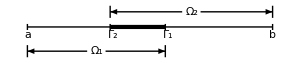

Generally speaking there are two types of domain decomposition methods. There are those that make use of overlapping domains, called Schwarz methods, and those that make use of non-overlapping domains. DecompositionNDSolveValue implements Schwarz methods. Schwarz methods work by solving the PDE not over the entire domain Ω but by solving the same PDE over overlapping subsets Ω_1 and Ω_2. In other words, instead of finding the solution u(x) in the entire domain the Schwarz methods try to find two solutions u_1(x) for x ∈ (a, γ_1) and u_2(x) for x ∈ (γ_2, b). The solutions  u_1 and u_2 are then stitched together to make the solution u. To be able to solve the PDE on the subdomains artificial Dirichlet boundary conditions are introduced at γ_1 and γ_2. u_1 and u_2 are coupled by the artificial Dirichlet conditions u_1(γ_1)=u_2(γ_1) and u_2(γ_2)=u_1(γ_2). The boundary conditions are satisfied through an iterative scheme which, supposing that the solution is zero and that u_2^(0) is given, might look like this:

Dirichlet boundary conditions (u^k)_g at Γ_g for iteration number k.

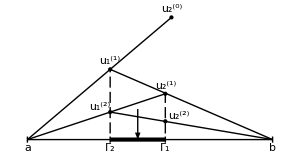

The figure gives an intuition for why, at least in this case, the convergence rate of Schwarz methods is dependent on the size of the overlap. More generally, one might have subdomains in a higher dimension. For example:

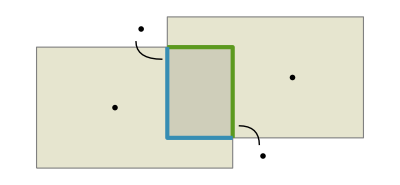

Here is a more formal description of the solution process. Consider the PDE, which can also have more general boundary conditions,
	Piecewise[{{Lu=f, on Ω}, {u=g, on ∂Ω}}]
where L is an elliptic differential operator, u is the dependent variable, Ω is the union of two subdomains Ω_1 and Ω_2, and ∂Ω is its boundary. A Schwarz method proceeds by first solving the PDE over Ω_1 using boundary conditions from the physical boundary ∂Ω_1\Γ_1 and an artificial Dirichlet boundary on Γ_1, with u_2^(0)given.

{ Lu_1^(k+1)=f | in Ω_1
u_1^(k+1)=u_2^(k) | on Γ_1
u_1^(k+1)=0 | on ∂Ω_1\Γ_1

Then, in a second step the PDE is solved over Ω_2 with boundary conditions from the physical boundary ∂Ω_2\Γ_2 and an artificial Dirichlet boundary condition on Γ_2 based on the solution u_1, the previous step

{ Lu_2^(k+1)=f | in Ω_2
u_2^(k+1)={w_1^(k+1)
w_1^(k) | on Γ_2
u_1^(k+1)=0 | on ∂Ω_2\Γ_2

The PDE is solved again over domain Ω_1, with an updated artificial boundary condition on Γ_1 form u_2. This iteration is continued k times until convergence is reached. u_1^(k) is the solution on Ω_1 after k iterations and u_2^(k) is the corresponding solution on Ω_2. Convergence means that u_1 agrees with u_2 on Γ_1 and Γ_2, which, it can be shown, is enough for u_1 and u_2 to agree with the global solution u throughout Ω. Γ_1and Γ_2, given in the figure, are called artificial boundaries. They are distinguished from the physical boundaries ∂Ω_1\Γ_1 and ∂Ω_2\Γ_2 because they don't exist in the original problem.

Note that the equation system represents two distinct algorithms: depending on the choice of the artificial boundary condition on Γ_2 in the second equation system. In the multiplicative Schwarz method, the artificial Dirichlet conditions of all subdomains are updated when the solution is updated in any other subdomain. By contrast, in the additive Schwarz method, the solutions are updated in each subdomain independently before updating the boundary conditions. The convergence rate of the additive Schwarz method is less than that of the multiplicative Schwarz method, but has the advantage of being inherently parallelized. The multiplicative Schwarz method is also known as alternating Schwarz algorithm in the case of two subdomains.

### Domain decomposition solvers

DecompositionNDSolveValue implements the one-level multiplicative Schwarz method and the one-level additive Schwarz method. It either uses or is used in conjunction with ElementMeshDecomposition, which is a function that splits a domain into a given number of subdomains with a specified amount of overlap. DecompositionNDSolveValue can use approximate solutions as a starting point in order to speed up convergence. It can also be run sequentially on one computer – which decreases the memory just as much as running the computations in parallel but is slower – or in parallel by making use of arbitrary kernel objects. In all of the following examples, keep in mind that multiplicative Schwarz is the default method used by DecompositionNDSolveValue. Except if kernels are specified, in which case DecompositionNDSolveValue will always use additive Schwarz as it is the only method it knows how to use in parallel.

We specify a model PDE that will be used in this section.

Set up a model PDE:

```mathematica
op=-Laplacian[u[x,y],{x,y}]-1;
bcs=DirichletCondition[u[x,y]==0,x==0||x==5||y==0||y==1];
Ω=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.0001];
```

#### The multiplicative and additive Schwarz methods

DecompositionNDSolveValue implements the multiplicative Schwarz method and the additive Schwarz method for sequential evaluation. They both have robust convergence and the same decrease in the amount of memory, but multiplicative Schwarz has a better convergence rate and is therefore faster when used sequentially (i.e. no kernels have been provided). The additive Schwarz method is inherently parallel, and it is currently the only algorithm available when using the Kernels option to solve problems in parallel.

Solve the equations with additive Schwarz and multiplicative Schwarz:

```mathematica
mem1=MaxMemoryUsed[{t1,sol1}=AbsoluteTiming@DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,Method->"AdditiveSchwarz","Tolerance"->0.001]];
mem2=MaxMemoryUsed[{t2,sol2}=AbsoluteTiming@DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,Method->"MultiplicativeSchwarz","Tolerance"->0.001]];
```

Make a table comparing the solutions:

```mathematica
TableForm[
N@{{mem1/10^6,mem2/10^6,mem2/mem1},{t1,t2,t1/t2}},
TableHeadings->{{"Memory (MB)","Timing (s)"}, {"Additive","Multiplicative","Additive/Multiplicative"}}
]
```

| Additive | Multiplicative | Additive/Multiplicative
Memory (MB) | 127.61 | 128.008 | 1.00312
Timing (s) | 27.5909 | 21.7946 | 1.26595

The example shows that multiplicative Schwarz and additive Schwarz consume the same amount of memory, but that multiplicative Schwarz is faster.

#### Adjusting the tolerance of the convergence criterion

DecompositionNDSolveValue stops iterating when the norm of the difference between the current and the previous solution vector is below a tolerance. The tolerance is by default 10^-6 but can be specified using the Tolerance option. MaxIterations can be used to specify that the iteration should stop after a certain number of iterations even if the solution has not converged based on the tolerance.

DecompositionNDSolveValue stops iteration when the norm falls below the given tolerance:

```mathematica
Ω=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.001];
DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->10^(-6),"EvaluationMonitor"->(Print[Norm[#-#2]]&)];
```

9.74968

0.299997

0.00361371

0.0000221103

1.15838×10^-7

The function used with EvaluationMonitor in this example is the same one that is used internally to determine whether to stop iterating. The printed values show that the last iteration is the first one for which the norm is below the tolerance threshold, which is how the decision whether to stop iterating is made. The choice of the number of subdomains and the amount of overlap will be discussed extensively later in this tutorial, for now it is enough to know that those values were chosen to make the convergence rate appropriate for the example.

MaxIterations can be used to force DecompositionNDSolveValue to stop after a specified number of iterations whether the solution has converged according to the specified tolerance threshold or not.

Using MaxIterations to stop DecompositionNDSolveValue before the solution has converged:

```mathematica
DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->10^(-6),"MaxIterations"->2,"EvaluationMonitor"->(Print[Norm[#-#2]]&)];
```

9.74968

0.299997

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 2 iterations.

#### Providing an approximate solution to speed up convergence

The computations can be sped up by making the Schwarz algorithm converge faster. There are two way to achieve a faster convergence:

Increase the overlap of the subdomains.

Provide an initial guess of the solution.

The better of an approximation of the actual solution that can be provided, the fewer iterations will have to be done to satisfy the tolerance criterion. The following example shows how to provide an initial guess.

Create a mesh and a coarse version of that mesh:

```mathematica
Ω=Rectangle[{0,0},{5,1}];
mesh=ToElementMesh[Ω,MaxCellMeasure->0.01];
coarseMesh=SetMaxCellMeasure[{Ω,Rectangle[{0,0},{5,1}]},0.1];
```

Find the solution using the coarse mesh:

```mathematica
coarseSolution=NDSolveValue[{op==0,bcs},u,{x,y}∈coarseMesh];
```

Count the number of iteration until convergence:

```mathematica
Length[Reap[DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈mesh,"DomainDecomposition"->{"Subdomains"->10,"Overlap"->5},"EvaluationMonitor"->Sow]][[2]]]
```

5

Count the number iterations it takes for the solution to converge when starting from the solution obtained using the coarse mesh:

```mathematica
Length[Reap[DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈mesh,"DomainDecomposition"->{"Subdomains"->10,"Overlap"->5},"InitialGuess"->coarseSolution,"EvaluationMonitor"->Sow]][[2]]]
```

3

The example shows that providing an estimate of the solution can decrease the number of iterations required for the solution to converge and therefore decrease the amount of time it takes to solve the problem. The code makes use of the function SetMaxCellMeasure, which takes a mesh and its corresponding symbolic region and creates a new, coarser mesh. It does this by pruning nodes in the body of the mesh while leaving the boundary nodes as they are, thus ensuring that the new mesh covers exactly the same space as the original mesh.

#### Solving problems in parallel using local or remote kernels

The additive Schwarz method can be used to parallelize the computation over several kernels. These can be local kernels, which is less useful because NDSolve is already parallelized, or remote kernels, for example in a computer cluster. To do this, simply launch the kernels and pass them to DecompositionNDSolveValue via the "Kernels" option.

Solve a problem in parallel using two local kernels:

```mathematica
kernels=LaunchKernels[2];
DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Rectangle[{0,0},{5,1}],"Kernels"->kernels]
```

InterpolatingFunction[…]

The additive Schwarz method is always used when kernels are provided, because it is very well suited as a parallel domain decomposition method. A parallel version of multiplicative Schwarz has not been implemented in this version. DecompositionNDSolveValue will divide the domain into as many subdomains as there are kernels. If subdomains are specified then the number of kernels should match the number of subdomains. DecompositionNDSolveValue cannot be used with fewer kernels than subdomains, if there are more kernels than subdomains then only the required number of kernels will be used. The subdomains are setup on one kernel each. Each kernel is responsible for solving the PDE over its subdomain once every iteration.  The first kernel in the list is matched with the first subdomain in the list and so on. This could be used to place a particularly large subdomain on a computer with more memory. Using a different number of kernels than subdomains will give an error message.

#### Monitoring the convergence of the solution

The option EvaluationMonitor can be used to evaluate a function after each iteration. The function is given as its first argument the current estimate of the solution and as its second argument the previous estimate of the solution. This can be used to, for example, visualize the progress of the solution, or to compute the norm of the difference between the two arguments to see how far away the norm is from dropping below the specified tolerance.

Monitor convergence using EvaluationMonitor:

```mathematica
sol2=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Rectangle[{0,0},{5,1}],"DomainDecomposition"->{"Subdomains"->2},"Tolerance"->10^(-6),"EvaluationMonitor"->(Print[Norm[#-#2]]&)];
```

2.79205

0.0121939

3.88446×10^-6

1.23719×10^-9

The example shows how the norm decreases iteration by iteration until it drops below the tolerance threshold.

#### Passing subdomain options to DecompositionNDSolveValue

If DecompositionNDSolveValue is given a region instead of subdomains (as given by ElementMeshDecomposition), it will try to split the region into an appropriate number of subdomains. The settings of ElementMeshDecomposition and ToElementMesh can be given through options to DecompositionNDSolveValue in the following way:

```mathematica
sol=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Rectangle[{0,0},{5,1}],"DomainDecomposition"->{
"MeshOptions"->{MaxCellMeasure->0.01},
"Subdomains"->2,
"Overlap"->5
}];
```

More information can be found in the documentation for ElementMeshDecomposition below.

#### DecompositionNDSolveValue options

The following table summarizes the options available for DecompositionNDSolveValue.

Method | "AdditiveSchwarz" or "MultiplicativeSchwarz"
"Kernels" | List of kernels. Additive Schwarz will automatically be used to solve the problem in parallel using the given kernels if this option is specified. The numer of kernels must match the number of subdomains.
"Tolerance" | Iteration will stop when the two-norm of the difference between the current solution and the solution in the previous iteration falls below this number.
"MaxIterations" | Iteration will stop if the number of iterations goes beyond this number.
"InitialGuess" | A list of functions, such as interpolation objects, representing an approximate solution to the given problem. This option can be used to speed up the time until convergence.
"EvaluationMonitor" | An arbitrary function that takes as its argument the current estimate of the solution.
"DomainDecomposition" | Used to pass options to SplitElementMesh and ToElementMesh
"LinearSolveMethod" | "Banded", "Cholesky", "Krylov", "MultiFrontal", or "Pardiso"

DecompositionNDSolveValue options.

### Scope of Schwarz algorithms as implemented in Wolfram Language

The currently available domain decomposition methods work for stationary, elliptic partial differential equations in one, two, and three dimensions. As a rule of thumb, any steady partial differential equation that the FEM package can solve, can also be solved with the Schwarz algorithms. Currently, only additive Schwarz is supported for solving PDEs in parallel.

The following example demonstrates that domain decomposition methods can handle equations with convection.

Set up the equation:

```mathematica
Ω=ToElementMesh[MengerMesh[3]];
pde={
Laplacian[u[x,y],{x,y}]+{1,10}.Grad[u[x,y],{x,y}]+1==0,
DirichletCondition[u[x,y]==0,x==0||x==1||y==0||y==1]
};
```

Solve convection-diffusion equation using NDSolve:

```mathematica
sol=NDSolveValue[pde,u,{x,y}∈Ω];
```

Solve convection-diffusion equation using DecompositionNDSolveValue:

```mathematica
sol2=DecompositionNDSolveValue[pde,u,{x,y}∈Ω];
```

Compare solutions:

```mathematica
Norm[sol2["ValuesOnGrid"]-sol["ValuesOnGrid"]]
```

6.65399×10^-8

The class of supported PDEs is not limited to systems of equations with one dependent variable as in the previous examples. This makes it possible to use the Schwarz algorithms for solving problems in, for example, structural mechanics. In the following problem, a force is pulling at the edge of a metal plate:

Set up the equations:

```mathematica
Ω=Rectangle[{0,0},{40 10^(-3),30 10^(-3)}];
pde={
({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive==NeumannValue[10^9,x==(40 10^(-3))],
({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive==0,
DirichletCondition[{u[x,y]==0,v[x,y]==0},x==0]
}/.{ν->0.3,Y->(200 10^9)};
```

Solve and visualize the coupled PDEs using NDSolve:

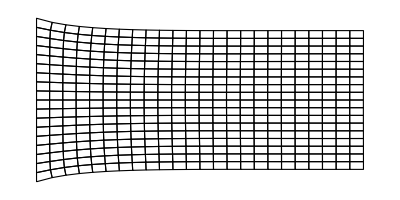

```mathematica
{ufun,vfun}=NDSolveValue[pde,{u,v},{x,y}∈Ω];
ElementMeshDeformation[ufun["ElementMesh"],{ufun,vfun},"ScalingFactor"->100]["Wireframe"[ImageSize->{Automatic,100}]]
```

Solve the coupled PDEs using DecompositionNDSolveValue:

```mathematica
{ufun2,vfun2}=DecompositionNDSolveValue[pde,{u,v},{x,y}∈Ω];

{Norm[ufun["ValuesOnGrid"]-ufun2["ValuesOnGrid"]],Norm[vfun["ValuesOnGrid"]-vfun2["ValuesOnGrid"]]}
```

{4.4865×10^-6,0.0000156342}

### What influences good convergence

The convergence rate of one-level Schwarz algorithms, which is the kind of Schwarz algorithms currently implemented, is known to deteriorate with an increasing number of subdomains. The reason is that subdomains only exchange information with their nearest neighbors.

Problem setup:

```mathematica
Ω=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.01];
op=-Laplacian[u[x,y],{x,y}]-1;
bcs=DirichletCondition[u[x,y]==0,x==0||x==5];
```

Solve the problem using NDSolve:

```mathematica
sol=NDSolveValue[{op==0,bcs},u,{x,y}∈Ω];
```

Solve the problem using 2 subdomains, overlap 4, and 50 iterations:

```mathematica
sol2=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->0,"MaxIterations"->50,"DomainDecomposition"->{"Subdomains"->2,"Overlap"->4}];
Norm[sol["ValuesOnGrid"]-sol2["ValuesOnGrid"]]
```

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 50 iterations.

4.84444×10^-12

Solve the problem using 5 subdomains, overlap 4, and 50 iterations:

```mathematica
sol3=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->0,"MaxIterations"->50,"DomainDecomposition"->{"Subdomains"->5,"Overlap"->4}];
Norm[sol["ValuesOnGrid"]-sol3["ValuesOnGrid"]]
```

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 50 iterations.

0.0000426103

Solve the problem using 10 subdomains, overlap 4, and 50 iterations:

```mathematica
sol4=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->0,"MaxIterations"->50,"DomainDecomposition"->{"Subdomains"->10,"Overlap"->4}];
Norm[sol["ValuesOnGrid"]-sol4["ValuesOnGrid"]]
```

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 50 iterations.

0.00409959

The previous examples show that 50 iterations yield a much better solution when there are fewer subdomains. This is because the convergence rate decreases with an increasing number of subdomains. The convergence rate can be improved in two ways; by increasing the amount of overlap, or by providing a better initial guess.

Solve the problem using 10 subdomains, overlap 20, and 50 iterations:

```mathematica
sol5=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->0,"MaxIterations"->50,"DomainDecomposition"->{"Subdomains"->10,"Overlap"->20}];
Norm[sol["ValuesOnGrid"]-sol5["ValuesOnGrid"]]
```

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 50 iterations.

3.62876×10^-13

Solve the problem using 10 subdomains, overlap 4, and 50 iterations, with an initial guess:

```mathematica
coarseMesh=SetMaxCellMeasure[{Ω,Rectangle[{0,0},{5,1}]},0.1];
coarseSolution=NDSolveValue[{op==0,bcs},u,{x,y}∈coarseMesh];
sol6=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"Tolerance"->0,"MaxIterations"->50,"DomainDecomposition"->{"Subdomains"->10,"Overlap"->4},"InitialGuess"->{coarseSolution}];
Norm[sol["ValuesOnGrid"]-sol6["ValuesOnGrid"]]
```

DecompositionNDSolveValue::maxiter: Failed to converge to the requested accuracy or precision within 50 iterations.

8.63297×10^-13

#### Monitoring convergence

Convergence can be monitored using the EvaluationMonitor option of DecompositionNDSolveValue. EvaluationMonitor assumes that its value is a function and evaluates it with two arguments; the first argument is the current estimate of the global solutions, and the second argument is the estimate of the global solutions from the previous iteration.

Monitor convergence using EvaluationMonitor:

```mathematica
sol2=DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"DomainDecomposition"->{"Subdomains"->2,"Overlap"->0.3},"Tolerance"->10^(-6),"EvaluationMonitor"->(Print[Norm[#-#2]]&)];
```

88.2919

2.99044

0.0400226

0.000535641

7.16874×10^-6

9.59415×10^-8

#### Specifying a method for LinearSolve

The finite element method discretizes partial differential equations and turns them into a linear equation system. The time and amount of memory it takes to solve a PDE using FEM is largely dependent on the solver used to solve the linear equations. Internally, LinearSolve is responsible for solving the discretized equations. DecompositionNDSolveValue's LinearSolveMethod can be used to pass a method to LinearSolve. "Pardiso" is the fastest and most memory efficient solver, and it is currently used as the default.

Set up equations:

```mathematica
op=-Laplacian[u[x,y],{x,y}]-1;
bcs=DirichletCondition[u[x,y]==0,x==0||x==1||y==0||y==1];
Ω=MengerMesh[5];
```

Solve the PDE using default solver:

```mathematica
MaxMemoryUsed[DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω]]
```

113850968

Solve the PDE using "Pardiso":

```mathematica
MaxMemoryUsed[DecompositionNDSolveValue[{op==0,bcs},u,{x,y}∈Ω,"LinearSolveMethod"->"Pardiso"]]
```

111530576

The smaller memory consumption means that it almost always makes sense to use Pardiso when trying to decrease memory consumption using domain decomposition methods.

### Subdomains

The preceding sections have talked about how to solve PDEs using domain decomposition methods. The details of how domains are decomposed into parts, subdomains, has not been discussed as it has been handled by DecompositionNDSolveValue. Sometimes it can be useful to decompose the element mesh separately without using DecompositionNDSolveValue. For example, to check what the subdomains look like, to inspect their properties, or even to implement custom domain decomposition methods. ElementMeshDecomposition is a function that takes an element mesh and returns a decomposition of that element mesh into subdomains. The subdomains can be queried to find information about the subdomain mesh properties and the relationships between the subdomains in terms of for example shared incidents, artificial boundary incidents, and physical boundary incidents. Subdomains returned by ElementMeshDecomposition can be given to DecompositionNDSolveValue in place of a region.

#### Creating subdomains using ElementMeshDecomposition

Any element mesh can be divided into subdomains using the ElementMeshDecomposition function.

Decompose a rectangle into two subdomains and visualize them:

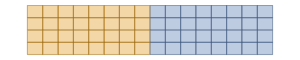

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.1];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->2,"Overlap"->0];
subdomains["Wireframe"[ImageSize->300]]
```

ElementMeshDecomposition has two options: "Subdomains" and "Overlap". Overlap is the number of layers one subdomain reaches into the neighboring subdomain. In the following example, four layers of elements overlap, which is two layers in each direction from the boundary in between the subdomains in the preceding example. That is, two layers in each direction from the boundary in between the corresponding nonoverlapping subdomains.

Specify two layers of elements of overlap:

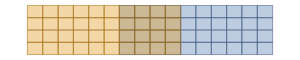

```mathematica
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->2,"Overlap"->2];
subdomains["Wireframe"[ImageSize->300]]
```

"Subdomains" specifies how many subdomains the region should be decomposed into. If an integer is given then ElementMeshDecomposition will attempt to split the element mesh into that many subdomains. If a list of fractions is given then it will try to decompose the element mesh into as many subdomains as there are elements in the list, each with approximately the specified fraction of the total area.

Decompose a Menger mesh into four subdomains with six layers of overlap:

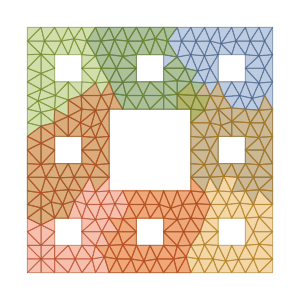

```mathematica
mesh=ToElementMesh[MengerMesh[2]];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->4,"Overlap"->6];
subdomains["Wireframe"[ImageSize->300]]
```

The figure shows four subdomains. The overlapping regions are given distinct colors as well.

Use a list of fractions to divide an element mesh into subdomains of different sizes:

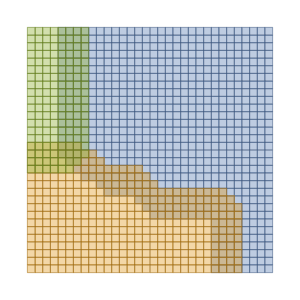

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{1,1}],MaxCellMeasure->0.001];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->{0.1,0.3,0.6},"Overlap"->2];
subdomains["Wireframe"[ImageSize->300]]
```

In the preceding example, the blue subdomain takes up roughly 60 % of the area, the yellow subdomain takes up roughly 30 % and the green subdomain takes up roughly 10 %. Subdomains of unequal sizes can be used to distribute the computational load unevenly across kernels if, for example, one kernel has access to more memory than another.

#### Set overlap as a fraction of the subdomain element graph diameter

Consider an undirected graph representing the connections between elements in a subdomain element mesh. It turns out that the convergence rate is related to the overlap as a percentage of the graph diameter. It is often easier to specify the amount of overlap as a fraction of the graph diameter than as a number of layers because of this. This can be done.

Set the overlap to 10 % of the graph diameter

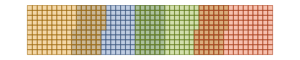

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.01];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->4,"Overlap"->0.05];
subdomains["Wireframe"[ImageSize->300]]
```

Use the same overlap specification for a mesh with more subdomains

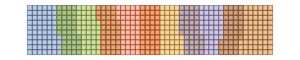

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.01];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->6,"Overlap"->0.05];
subdomains["Wireframe"[ImageSize->300]]
```

Use the same overlap specification for a mesh with more mesh elements

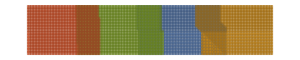

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.001];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->4,"Overlap"->0.05];
subdomains["Wireframe"[ImageSize->300]]
```

The examples show that specifying the overlap as a fraction of the subdomain graph diameter is a good way of ensuring that the overlap will adapt if the number of elements in the subdomains changes.

#### Specifying overlap for subdomains individually

The subdomains used so far have all extended themselves into their neighbors by approximately same number of layers. It is also possible specify the number of layers for each subdomain individually.

Set overlap to zero for the subdomains in the middle, 20 for the ones at the edge:

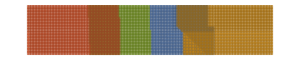

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.001];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->4,"Overlap"->{0,20,0,20}];
subdomains["Wireframe"[ImageSize->300]]
```

#### One-dimensional and three-dimensional examples

It is not just two-dimensional domains which can be decomposed by ElementMeshDecomposition, but also one-dimensional and three-dimensional domains.

Decomposing a one-dimensional domain into subdomains:

```mathematica
mesh=ToElementMesh["Coordinates"->Partition[Range[0.,1.,1/9],1], "MeshElements"->{LineElement[{{1, 2}, {2, 3}, {3, 4}, {4, 5}, {5, 6}, {6, 7}, {7, 8}, {8, 9}, {9, 10}}]}];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->2,"Overlap"->0]
```

SubdomainGroup[<2>]

Decomposing a three-dimensional domain into subdomains:

```mathematica
reg=Cuboid[{0,0,0},{10,15,24}];
reg=RegionDifference[reg,Cuboid[{3,0,3},{10,15,105/10}]];
reg=RegionDifference[reg,Cuboid[{0,0,135/10},{7,15,21}]];
mesh=ToElementMesh[reg,RegionBounds[reg]];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->6,"Overlap"->0];
subdomains["Wireframe"[ImageSize->300]]
```

-Graphics3D-

#### Subdomain wireframe visualization

Visualizing subdomains is very similar to visualizing regular element mesh objects, which is described in Element Mesh Visualization. Domain decompositions have the same familiar properties:

subdomains["Wireframe"] | show a superposition of colored wireframes
subdomains["Wireframe"[pos]] | show the subdomains having positions corresponding to the list of positions pos.

SubdomainGroup wireframe commands.

"Wireframe" accepts the following options, which are the same for subdomains as it is for ElementMesh:

"MeshElement" | specifies which mesh element should be drawn
"MeshElementIDStyle" | specifies the style with which the mesh element ID should be drawn
"MeshElementMarkerStyle" | specifies the style with which the mesh element marker should be drawn
"MeshElementStyle" | specifies the style with which the mesh elemnt should be drawn

Options for "Wireframe" visualization of subdomains.

Any options accepted by Graphics will also be applied to the wireframe.

Using the ImageSize option of Graphics to set the size of the resulting graphics:

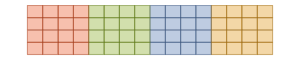

```mathematica
mesh=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.1];
subdomains=ElementMeshDecomposition[mesh,"Subdomains"->4,"Overlap"->0];
subdomains["Wireframe"[ImageSize->300]]
```

Specify an edge color for all elements regardless of subdomain:

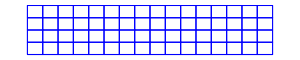

```mathematica
subdomains["Wireframe"["MeshElementStyle"->EdgeForm[Blue],ImageSize->300]]
```

Lists can be used to specify different options for different subdomains. The list will repeat itself cyclically if the number of stylings in the list is shorter than the number of subdomains.

Style specifications are reused cyclically:

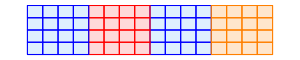

```mathematica
subdomains["Wireframe"[
"MeshElementStyle"->{
Directive[FaceForm[LightBlue],EdgeForm[Blue]],
Directive[FaceForm[LightOrange],EdgeForm[Orange]],
Directive[FaceForm[LightRed],EdgeForm[Red]]},
ImageSize->300]]
```

#### Subdomain data structures

The structure of the object returned by ElementMeshDecomposition is SubdomainGroup[mesh, {Subdomain[...], Subdomain[...], ...}] where mesh corresponds to the global domain. The Subdomain and  SubdomainGroup objects have properties. These properties can be used to implement custom domain decomposition methods. They are listed below.

Mesh | original mesh
Subdomains | subdomain objects
Properties | list of subdomain group properties

Subdomain group properties.

Mesh | subdomain mesh
Coordinates | subdomain mesh coordinates
Incidents | mesh incidents
InteriorIncidents | incidents which do not belong to the boundary
BoundaryIncidents | incidents which belong to the boundary
ArtificialBoundaryIncidents | incidents which belong to the artificial boundary
SharedIncidents | incidents which other subdomains rely on
LocalToGlobal | association which maps local incidents to global incidents
Properties | list of subdomain properties

Subdomain properties.

The corresponding incidents in the global mesh are given by the following properties. This is the same as applying the mapping given by LocalToGlobal to the local incidents.

GlobalIncidents | Global subdomain mesh incidents
GlobalInteriorIncidents | Global subdomain interior incidents
GlobalBoundaryIncidents | Global subdomain boundary incidents
GlobalArtificialBoundaryIncidents | Global subdomain artificial boundary
GlobalSharedIncidents | Global subdomain shared incidents

Global incidents subdomain properties.

#### Global versus local incidents

Because each subdomain has fewer incidents than the full mesh the subdomain incidents do not match up with the list of coordinates in the full mesh. This means that two sets of incidents are needed to, say, map the solution vector of a subdomain onto the solution vector of the full mesh. Each type of incident is therefore provided both as local incidents and global incidents. A map is also provided which maps local incidents into global incidents.

Create two subdomains:

```mathematica
Ω=ToElementMesh[Rectangle[{0,0},{5,1}],MaxCellMeasure->0.1];
subdomains=ElementMeshDecomposition[Ω,"Subdomains"->2,"Overlap"->2];
subdomains["Wireframe"[ImageSize->300]]
```

-Graphics-

Find the coordinates of the artificial boundary using a global mesh:

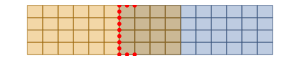

```mathematica
{s1,s2}=subdomains["Subdomains"];
coords=Part[Ω["Coordinates"],s1["GlobalArtificialBoundaryIncidents"]];
Show[
subdomains["Wireframe"[ImageSize->300]],
Graphics[{PointSize[Large],Red,Point[coords]}]
]
```

Find the coordinates of the artificial boundary using a subdomain mesh:

```mathematica
{s1,s2}=subdomains["Subdomains"];
coords=Part[s1["Coordinates"],s1["ArtificialBoundaryIncidents"]];
Show[
subdomains["Wireframe"[ImageSize->300]],
Graphics[{PointSize[Large],Red,Point[coords]}]
]
```

-Graphics-

The difference between the first way of getting the boundary incidents and the second is that the incidents are retrieved using the GlobalArtificialBoundaryIncidents property in the first example, and ArtificialBoundaryIncidents in the second example. As always, incidents correspond to coordinates, but in this case they correspond to coordinates in different element mesh objects. The list GlobalArtificialBoundaryIncidents corresponds to coordinates in the full mesh and ArtificialBoundaryIncidents corresponds to elements in the local mesh. In the next example it is shown how incidents retrieved using ArtificialBoundaryIncidents can be converted into incidents that can be used with the coordinates of the full mesh.

How to convert local incidents into global incidents:

```mathematica
{s1,s2}=subdomains["Subdomains"];
coords=Part[Ω["Coordinates"],s1["LocalToGlobal"]/@s1["ArtificialBoundaryIncidents"]];
Show[
subdomains["Wireframe"[ImageSize->300]],
Graphics[{PointSize[Large],Red,Point[coords]}]
]
```

-Graphics-

### Implementing domain decomposition methods

Some domain decomposition methods can be implemented at the top level, using ElementMeshDecomposition and NDSolve. The following is an implementation of the alternating Schwarz method, which is the multiplicative Schwarz method in the case of two subdomains.

Problem setup:

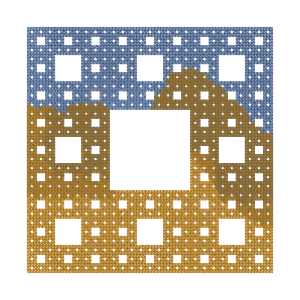

```mathematica
op = -Laplacian[u[x, y], {x, y}] - 1;
bcs = DirichletCondition[u[x, y] == 0, x==0||x==1||y==0||y==1];

mesh = ToElementMesh[MengerMesh[4]];
subdomains = ElementMeshDecomposition[mesh, "Subdomains" -> 2, "Overlap" -> 30];
subdomains["Wireframe"[ImageSize -> 300]]
```

Extract subdomain mesh properties:

```mathematica
{s1,s2}=subdomains["Subdomains"];
mesh1=s1["Mesh"];
mesh2=s2["Mesh"];
dof=Length[mesh["Coordinates"]];
dof1=Length[s1["Coordinates"]];
dof2=Length[s2["Coordinates"]];
```

Initialize local and global solution vectors:

```mathematica
uglobal=ConstantArray[0,dof];
u1=ConstantArray[0,dof1];
u2=ConstantArray[0,dof2];
```

Extract incident data from subdomains:

```mathematica
ab1=s1["ArtificialBoundaryIncidents"];
ab2=s2["ArtificialBoundaryIncidents"];
gab1=s1["GlobalArtificialBoundaryIncidents"];
gab2=s2["GlobalArtificialBoundaryIncidents"];
li1=s1["InteriorIncidents"];
li2=s2["InteriorIncidents"];
gi1=s1["GlobalInteriorIncidents"];
gi2=s2["GlobalInteriorIncidents"];
```

Implementation of the Alternating Schwarz method:

```mathematica
dirichletCondition=DirichletCondition[u[x,y]==#,"ElementIncidents"->{{#2}}]&;

Do[
bcs1=MapThread[dirichletCondition,{Part[uglobal,gab1],ab1}];
u1=NDSolveValue[{op==0,Prepend[bcs1,bcs]},u,{x,y}∈mesh1]["ValuesOnGrid"];
uglobal[[gi1]]=u1[[li1]];

bcs2=MapThread[dirichletCondition,{Part[uglobal,gab2],ab2}];
u2=NDSolveValue[{op==0,Prepend[bcs2,bcs]},u,{x,y}∈mesh2]["ValuesOnGrid"];
uglobal[[gi2]]=u2[[li2]];
,
{10}
];
```

The alternating Schwarz method solves the partial differential equation described in the introduction, where the mathematical details of the alternating Schwarz method are provided, using NDSolve.

Compare solution with NDSolve:

```mathematica
sol=NDSolveValue[{op==0,bcs},u,{x,y}∈mesh]["ValuesOnGrid"];
Norm[uglobal-sol]
```

5.80021×10^-13

Visualize the solution using ElementMeshInterpolation and Plot3D:

```mathematica
interp=ElementMeshInterpolation[{mesh},uglobal];
Plot3D[interp[x,y],{x,y}∈mesh,ImageSize->300]
```

-Graphics3D-

### Possible issues

DecompositionNDSolveValue may not be able to solve some PDEs with discontinuous coefficients.

Set up equations:

```mathematica
Ω=ToElementMesh[Disk[]];
Subscript[Γ, D]=DirichletCondition[u[x,y]==0,x≥0];
c=If[x^2+y^2≤1/4,{{10,0},{0,10}},{{1,0},{0,1}}];
op=Inactive[Div][(-c.Inactive[Grad][u[x,y],{x,y}]),{x,y}]-1;
```

Solve using NDSolve:

```mathematica
sol=NDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω];
```

Solve using DecompositionNDSolveValue:

```mathematica
sol2=DecompositionNDSolveValue[{op==0,Subscript[Γ, D]},u,{x,y}∈Ω,"DomainDecomposition"->{"Subdomains"->2,"Overlap"->10},"Tolerance"->10^(-10)];
```

Compare solutions:

```mathematica
Norm[sol2["ValuesOnGrid"]-sol["ValuesOnGrid"]]
```

1.71154

### References

Toselli, Andrea, and Olof Widlund. Domain Decomposition Methods - Algorithms and Theory. Springer, 2010.

Mathew, Tarek P. A. Domain Decomposition Methods for the Numerical Solution of Partial Differential Equations. Springer, 2008.

Related Tutorials